```mathematica
f[x_]:=1/20 x^4-x^2-x+10
y[x_,n_]:=10/NIntegrate[f[y]^n,{y,-5,5}] NIntegrate[f[y]^n,{y,-5,x}]-5
```

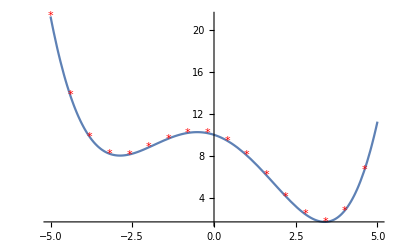

```mathematica
Show[
Plot[f[x],{x,-5,5}],
ListPlot[Table[{x,f[x]},{x,-5,5,0.6}],PlotMarkers->"*",PlotStyle->Red]
]
```

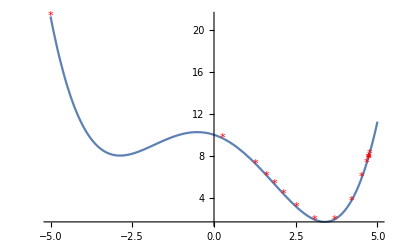

```mathematica
With[{n=4},
Show[
Plot[f[x],{x,-5,5}],
ListPlot[Table[{y[x,n],f[y[x,n]]},{x,-5,5,0.6}],PlotMarkers->"*",PlotStyle->Red]
]]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

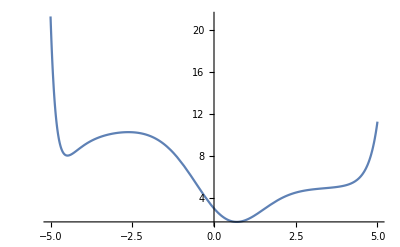

```mathematica
Plot[f[Evaluate@y[x,2]],{x,-5,5}]
```